## 4. phase response curve

### (a)

```mathematica
xdot=1/τ(v-ω n-(v^2+n^2)v)/.{v->x,n->y};
ydot=1/τ(ω v+n-(v^2+n^2)n)/.{v->x,n->y};
```

```mathematica
params={τ->1,ω->.3};
xmin=-2;xmax=2;ymin=-2;ymax=2;
cmap="LightTerrain";
```

A dense vector-flow plot :

```mathematica
vplottor[PARAMS_]:=
(
xres=yres=512;
VPLOT=LineIntegralConvolutionPlot[
{{xdot,ydot}/.PARAMS,{Automatic,xres,yres}},
{x,xmin,xmax},{y,ymin,ymax},
ColorFunction->cmap,
LineIntegralConvolutionScale->3,
LightingAngle->180,
AxesLabel->{"x","y"}
];
Return[VPLOT];
)
```

```mathematica
vplot=vplottor[params];
```

A less - dense explicit vector field (quiver) plot :

```mathematica
splottor[PARAMS_]:=
(
(*vector norms for making a color bar*)
values=Flatten[Table[
Table[
Sqrt[xdot^2+ydot^2]/.params/.{x->xval,y->yval},
{xval,xmin,xmax}
],
{yval,ymin,ymax}
]];
minv=Min[values];
maxv=Max[values];
SPLOT=StreamPlot[
{xdot/.PARAMS,ydot/.PARAMS},
{x,xmin,xmax},{y,ymin,ymax},
StreamColorFunction->cmap,
StreamPoints->Fine,
(*AxesLabel->{"x","y"},*)
PlotLegends->{BarLegend[
{cmap,{minv,maxv}},
LegendLabel->(SqrtBox[(ẋ)^2+(ẏ)^2]//DisplayForm)
]},
ImageSize->Large
];
Return[SPLOT];
)
```

```mathematica
splot=splottor[params];
```

Only the origin is a fp:

```mathematica
xsolns=Solve[{xdot==0,ydot==0},{x,y}]
```

{{x→0,y→0}}

```mathematica
(*Scatter plot at the fixed point (origin):*)
xx=x/.xsolns/.params;
yy=y/.xsolns/.params;
scatter[xlist_,ylist_,color_]:=
(
data=Transpose@{xlist,ylist};
Return[ListPlot[
data,
PlotStyle->{PointSize[Large],color},
AxesLabel->{"x","y"}
]];
);
listplot=scatter[xx,yy,White];
```

```mathematica
(*Combine them all in one plot:*)
title=StringForm["μ_1=`` μ_2=``",u1,u2];
Print[title];
shown=Show[
vplot,listplot,splot,
ImageSize->Large,
AxesLabel->{"x","y"},
PlotLabel->title
]
```

μ_1=u1 μ_2=u2

-Graphics-

Using polar coordinates:

```mathematica
xdot=1/τ(v-ω n-(v^2+n^2)v)/.{v->x,n->y};
ydot=1/τ(ω v+n-(v^2+n^2)n)/.{v->x,n->y};
```

```mathematica
radialize={x->r Cos[θ],y->r Sin[θ]};
Simplify[xdot/.radialize]
Simplify[ydot/.radialize]
```

-(r ((-1+r^2) Cos[θ]+ω Sin[θ]))/τ

(r (ω Cos[θ]+Sin[θ]-r^2 Sin[θ]))/τ

```mathematica
radialSys=Flatten[Solve[
{
-r Sin[θ] TDOT+RDOT Cos[θ]==(xdot/.radialize),
r Cos[θ] TDOT+RDOT Sin[θ]==(ydot/.radialize)
},
{RDOT,TDOT}
]];
```

```mathematica
rdot=Simplify[RDOT/.radialSys]
θdot=TDOT/.radialSys
```

(r-r^3)/τ

ω/τ

(Fixed points of the r equation are 0 and 1, for any parameters)

This is separable.

```mathematica
ROFT=r[t]/.DSolve[r'[t]==(r[t]-r[t]^3)/τ,r[t],t][[2]];
TOFT=θ[t]/.DSolve[θ'[t]==θdot,θ[t],t][[1]];
```

Set initial conditions as r_0, θ_0:

```mathematica
roft=ROFT/.Solve[r0==(ROFT/.t->0),C[1]][[1]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

ⅇ^(t/τ)/(√(-1+ⅇ^((2 t)/τ)+1/r0^2))

```mathematica
θoft=TOFT/.Flatten[Solve[θ0==(TOFT/.t->0),C[1]]]
```

θ0+(t ω)/τ

{}

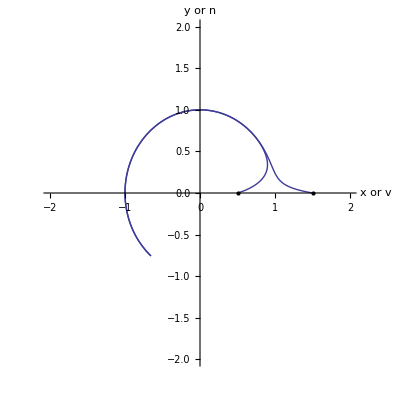

```mathematica
plots={}
For[i=1,i≤2,i++,(*Two ICs*)
R0={.5,1.5}[[i]];
T0=0;
p1=ParametricPlot[{roft Cos[θoft],roft Sin[θoft]}/.{r0->R0,θ0->T0,τ->1,ω->.2},{t,0,20}];
AppendTo[plots,p1];
p2=scatter[{R0 Cos[T0]},{R0 Sin[T0]},Black];
AppendTo[plots,p2];
];
Show[plots,PlotRange->{{-2,2},{-2,2}},
AxesLabel->{"x or v", "y or n"}]
```

Isochrons should be perpendicular to the flow. This is essentially a singular-perturbation/boundary-layer problem. If I remembered how to work those, perhaps my answer would be better. However, the presense of this boundary layer where flow is essentially parallel to the limit cycle, and the bulk region, where flow is closer to perpendicular to the LC, should be the cause of different regimes of z(θ) behavior.

When trajectories are quickly drawn onto the slow limit cycle (ω≪1), trajectories are essentially radii, and isocrons are essentially concentric circles, up to a very thin BL near the LC, where the isocrons transition to being perpendicular to the LC. An impulsive Δx will maximally affect θ at θ=-π, minimally at θ=π, and will have no effect at θ∈{0, 2π}. So the expected form is z(θ)=-sin(θ).

```mathematica
splottor[{τ->1,ω->.09}]
```

-Graphics-

For faster rotation, trajectories spiral more strongly, and it is harder to make an argument from inspection.

```mathematica
splottor[{τ->1,ω->3.0}]
```

-Graphics-

In order to use our r(t), θ(t) solutions, define require that r be within 1% of its steady-state value of 1before we can say we’re on the limit cyle after an impulsive Δx took us off. The strategy is then:
(1) start at (x,y) = (cosθ, sinθ)
(2) perturb to (x+Δx, y)
(3) for the initial condition r0=√[(x+Δx)^2+y^2] find T s.t. .99<r(t)<1.01
(4) for the initial condition θ0 = atan(y/(x+Δx)] find θ(T)
(5) take the limit of (θ(T)-θ0) / Δx as Δx→0
There will multiple solutions due to periodicity, but we can ignore these. The solution might be different, however, for perturbations inside and outside the LC.

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

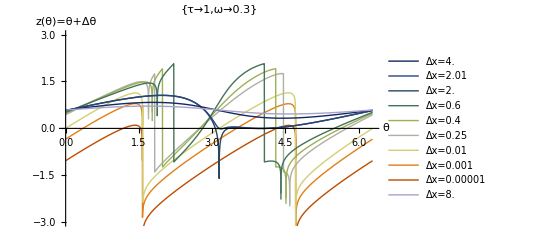

```mathematica
R0=Sqrt[(x+Δx)^2+y^2];
ROFT=(roft/.{r0->R0});
T1=t/.Solve[1.01==ROFT,t][[2]];
T2=t/.Solve[.99==ROFT,t][[2]];
θT1=Simplify[θoft/.{θ0->ArcTan[y/(x+Δx)],t->T1}/.radialize];
θT2=Simplify[θoft/.{θ0->ArcTan[y/(x+Δx)],t->T2}/.radialize];
(*For a given θ, I only expect one of these to be real.*)
θT={θT1,θT2};
plots={};
dxdx={.00001,.001,.01,.25,.4,.6,2.0,2.01,4.0,8.0};
For[i=1,i≤Length[dxdx],i++,
dx=dxdx[[i]];
pl=Plot[θT/.{r->1,Δx->dx}/.params,{θ,0,2π},
PlotStyle->{ColorData[40,"ColorList"][[i]],Thick},
PlotLegends->{StringForm["Δx=``",dx]}
];
AppendTo[plots,pl];
]
Show[
plots,
AxesLabel->{"θ","z(θ)=θ+Δθ"},
PlotLabel->params,
PlotRange->{Automatic,{-3,3}}
]
```

```mathematica
ColorData["Physical"]
```

{BlackBodySpectrum,HypsometricTints,VisibleSpectrum}

Weird things happen if you perturb past half or full radius.  For very large Δx (around 2), the discontinuities in z(θ) disappear.

```mathematica
θT/.{r->1}
```

{ArcTan[Sin[θ]/(Δx+Cos[θ])]+ω Log[(√(0.+50.7512 Δx^2+101.502 Δx Cos[θ]))/(√(1.+1. Δx^2+2. Δx Cos[θ]))],ArcTan[Sin[θ]/(Δx+Cos[θ])]+ω Log[(√(0.-49.2513 Δx^2-98.5025 Δx Cos[θ]))/(√(1.+1. Δx^2+2. Δx Cos[θ]))]}

This expression does not contain τ

```mathematica
Limit[θT/.{r->1},Δx->0]
```

{ω (-∞),ω (-∞)}

That didn’t go very well. I’ll have to fix this later.

```mathematica
Limit[θT/.{r->1},Δx->∞]
```

{1.96347 ω,(1.94847+1.5708 ⅈ) ω}